```mathematica
L1 = SetPrecision[13.5801271057617, 13];
L2 = SetPrecision[0.633743503720863, 15];
C1 = SetPrecision[1.1851951029611*^-05, 14];
C2 = SetPrecision[1.21570928814417*^-05, 14];
R1 = SetPrecision[112.110238762156, 12];
R2 = SetPrecision[39.6267299674116, 13];
R3 = SetPrecision[1049.73154916044, 11];
R4 = SetPrecision[519.38094143109, 11];
n = 8192;
δt = SetPrecision[0.0196349540849362, 16];
t = δt n;
Z1[ω_] = R4 + 1/(I ω C2);
Z2[ω_] = 1/(I ω C1)+R2 + I ω L2 + R3;
Zparallel[ω_] =1/(1/Z1[ω]+1/Z2[ω]);
I1[ω_] = Uin/(R1 + I ω L1 + Zparallel[ω]);
Uparallel[ω_] = I1[ω] Zparallel[ω];
Ipar2[ω_] = Uparallel[ω]/Z2[ω];
Uout[ω_] = Ipar2[ω]*R2;
H[ω_] = Uout[ω]/Uin;
```

Построение АЧХ

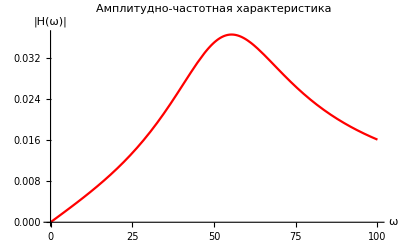

```mathematica
AFCh = Plot[Abs@H[ω],{ω,0,100}, AxesLabel->{"ω","|H(ω)|"}, PlotLabel->"Амплитудно-частотная характеристика", PlotStyle->{Red}]
```

Построение графика сигнала

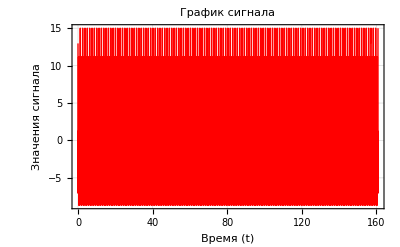

```mathematica
signal = Flatten[Import["C:\\Users\\22153\\Documents\\ЛЭТИ\\ФОИТ\\IDZ3\\Сигналы\\20.txt", "Table"]];
signalTable = Table[{(i-1 ) δt,signal[[i]]},{i,1,n}];
headers={"t","U(t)"};
table = Grid[Prepend[signalTable,headers],Frame->All,Alignment->Center,Background->{{LightRed,None},{LightGreen,None}}];
table;
ListLinePlot[signalTable,FrameLabel->{"Время (t)","Значения сигнала"},PlotLabel->"График сигнала",Frame->True,GridLines->Automatic,PlotStyle->{Red, Thin}]
```

Построение спектра

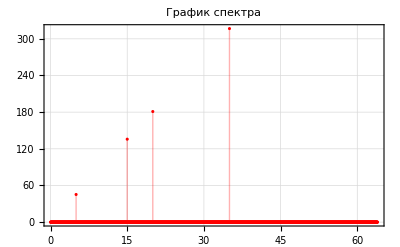

```mathematica
signalFourier = Fourier[signal];
outN  = Length@signalFourier;
df = 1 / t;
FourierAbs=Table[{2 π df (i-1),Abs@signalFourier [[i]]},{i,1,outN/5}];
ListPlot[FourierAbs,Filling->Axis,PlotRange->Full, PlotLabel->"График спектра",Frame->True,GridLines->Automatic,PlotStyle->{Red, Thin}]
```

Изменение 3 гармоники

0.01027569875

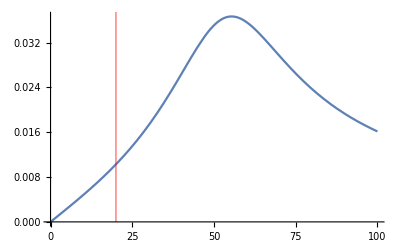

```mathematica
Abs@H[20]
Show[Plot[Abs@H[ω],{ω, 0, 100}], ListPlot[{{20, 3}}, Filling->Axis, PlotStyle->{Red}]]
```